```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression];Length[deps2]
```

1365053

```mathematica
changes2=Map[{Chrom[#[[1]]]/24,Chrom[#[[2]]]/24, #[[1]],#[[2]],#[[3]]}&,deps2];Length[changes2]
```

1365053

```mathematica
Take[changes2,3]
```

{{1,1,1,2,{2,1<->4,2<->3}},{1,1,2,3,{2,2<->4,3<->5}},{1,4,2,4,{2,2<->5,1<->4}}}

```mathematica
Length[StartMpg]
```

11

```mathematica
Table[{k,VertexCount[ReadGrof[StartMpg[[k]]]],VertexCount[ReadGrof[EndMPG[[k]]]]},{k,1,10}]
```

{{1,4,5},{2,6,6},{3,7,7},{4,8,8},{5,9,9},{6,10,10},{7,11,11},{8,12,12},{9,13,13},{10,14,14}}

## Graphs that go from 1 to Jacobsthal in one Rule 2 transform

```mathematica
championMoves=Flatten[
Table[
Select[
Take[changes2,{StartMpg[[k]],EndMPG[[k]]}],
#[[1]]==1 && #[[2]]==Jacobsthal[[k+1]]&
],{k,3,10}],1]
```

{{1,4,3,6,{2,2<->5,1<->6}},{1,5,5,11,{2,3<->5,4<->7}},{1,12,13,37,{2,3<->5,4<->7}},{1,21,22,72,{2,3<->5,1<->4}},{1,44,73,305,{2,3<->5,1<->4}},{1,85,306,1554,{2,3<->5,1<->4}},{1,172,1555,9149,{2,3<->5,1<->4}},{1,341,9150,58715,{2,3<->5,1<->4}}}

```mathematica
{1,1,3,8,"{2,2<->6,3<->5}"}
```

```mathematica
Map[
{Read[StringToStream[#[[5]]]][[2]]}&,Take[championMoves,-2]
]
```

{{3<->5},{3<->5}}

```mathematica
Criterion[3<->5,3<->5]
```

x3==1&&x5==2&&x3==3

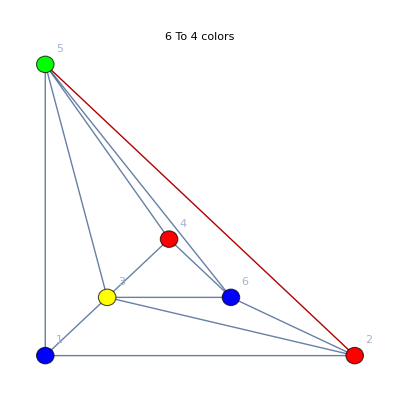
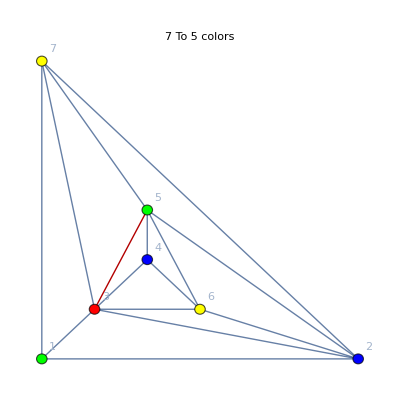
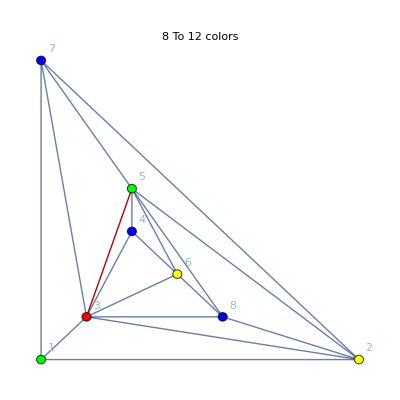
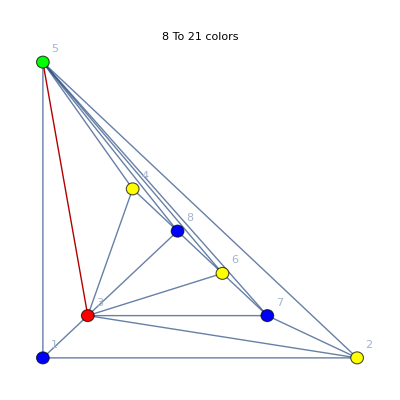
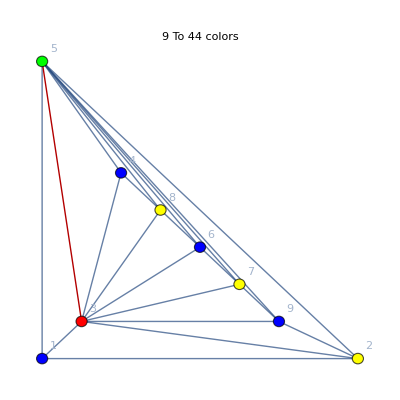
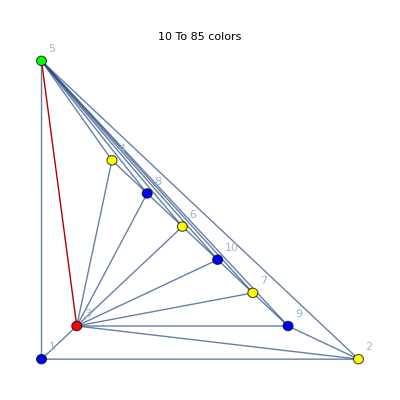
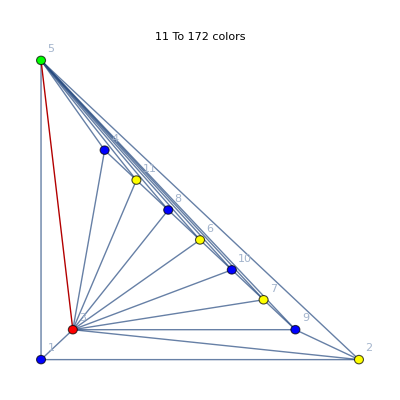
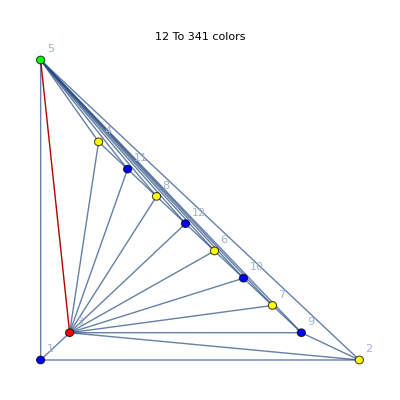

```mathematica
Map[
With[
{vars=Read[StringToStream[#[[5]]]]},
PaintGraph2First[ReadGrof[#[[3]]],Criterion[vars[[2]],vars[[3]]],VertexLabels->"Name", 
ImageSize->400,
GraphHighlight->{vars[[2]]},
PlotLabel->ToString[VertexCount[ReadGrof[#[[3]]]]]<>" To "<> ToString[#[[2]]]<>" colors "]
]&,
championMoves
]
```

```mathematica
Sort[EdgeList[Rule2[ReadGrof[9150],3<->5,1<->4]]]
```

{1<->2,1<->3,1<->5,1<->13,2<->3,2<->5,2<->9,3<->4,3<->6,3<->7,3<->8,3<->9,3<->10,3<->11,3<->12,3<->13,4<->5,4<->11,4<->13,5<->6,5<->7,5<->8,5<->9,5<->10,5<->11,5<->12,5<->13,6<->10,6<->12,7<->9,7<->10,8<->11,8<->12}

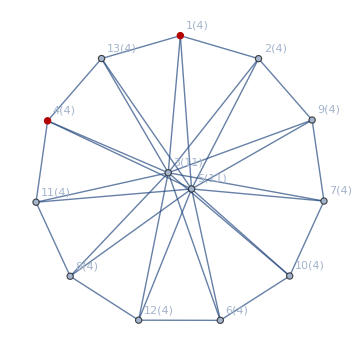
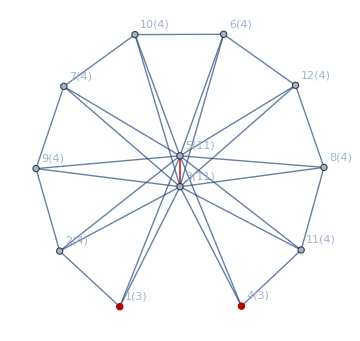

```mathematica
{With[
{g=Rule2[ReadGrof[9150],3<->5,1<->4]},
Graph[g, VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}],GraphHighlight->{1,4,3<->5},ImageSize->Medium]
],With[
{g=ReadGrof[9150]},
Graph[g, VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}], GraphHighlight->{1,4,3<->5},ImageSize->Medium]
]}
```

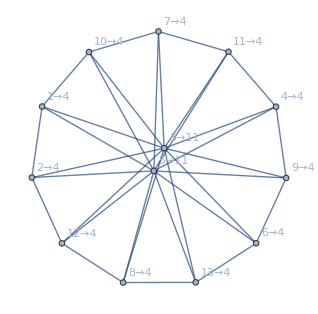
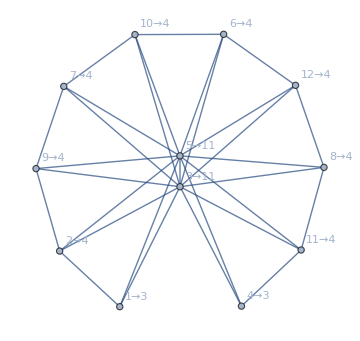

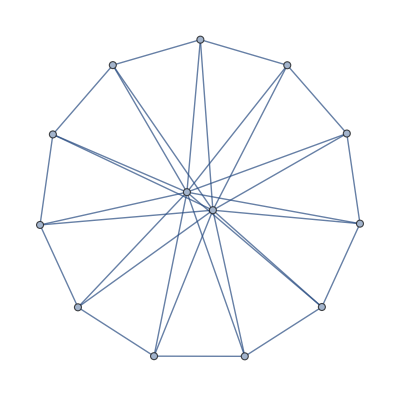

```mathematica
Rule2[ReadGrof[9150],3<->5,1<->4]
```

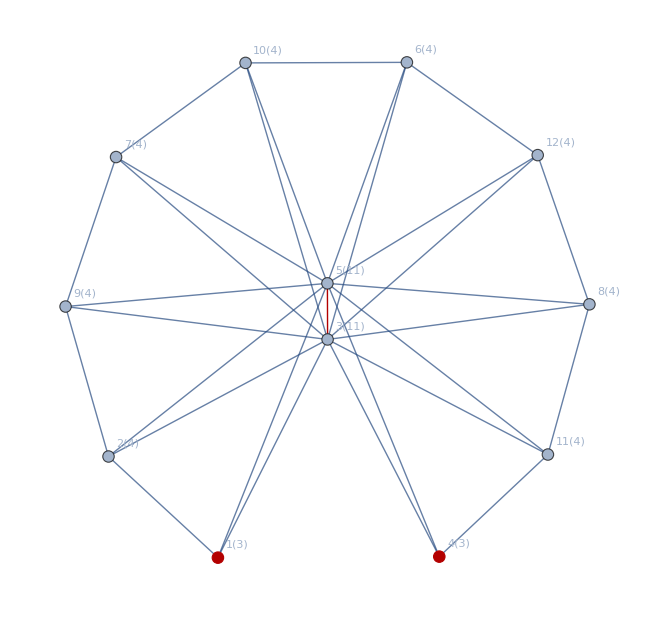

```mathematica
With[
{g=ReadGrof[9150]},
Graph[g, VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}], GraphHighlight->{1,4,3<->5}]
]
```

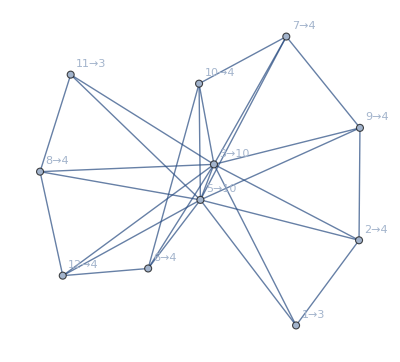

```mathematica
With[
{g=VertexDelete[ReadGrof[9150],4]},
Graph[g, VertexLabels->Table[v->{v->EdgeCount[g,v<->_]},{v,VertexList[g]}]]
]
```

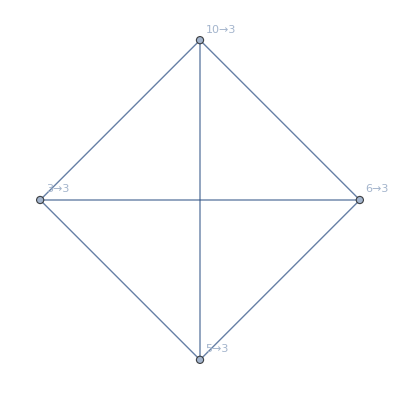

```mathematica
With[
{g=VertexDelete[ReadGrof[9150],{1,4,11,2,9,8,12,7}]},
Graph[g, VertexLabels->Table[v->{v->EdgeCount[g,v<->_]},{v,VertexList[g]}]]
]
```

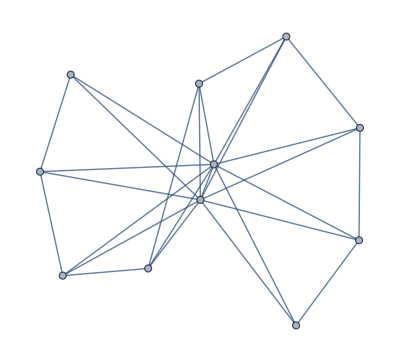

```mathematica
VertexDelete[ReadGrof[9150],4]
```

```mathematica
IsomorphicGraphQ[VertexDelete[ReadGrof[9150],{1,4,11,2,9,8,12}],CompleteGraph[4]]
```

False

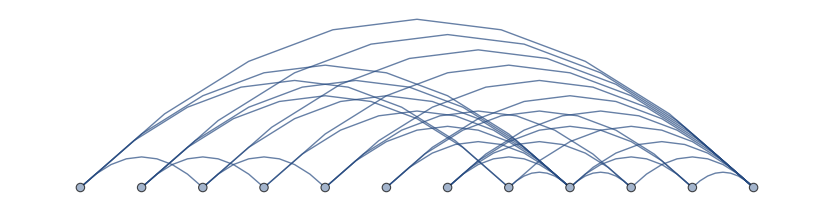

```mathematica
Graph[ReadGrof[9150],GraphLayout->"LinearEmbedding"]
```

```mathematica
Graph[JacobsThalGraph[9], GraphHighlight->{3<->4}, VertexLabels->"Name"]
```

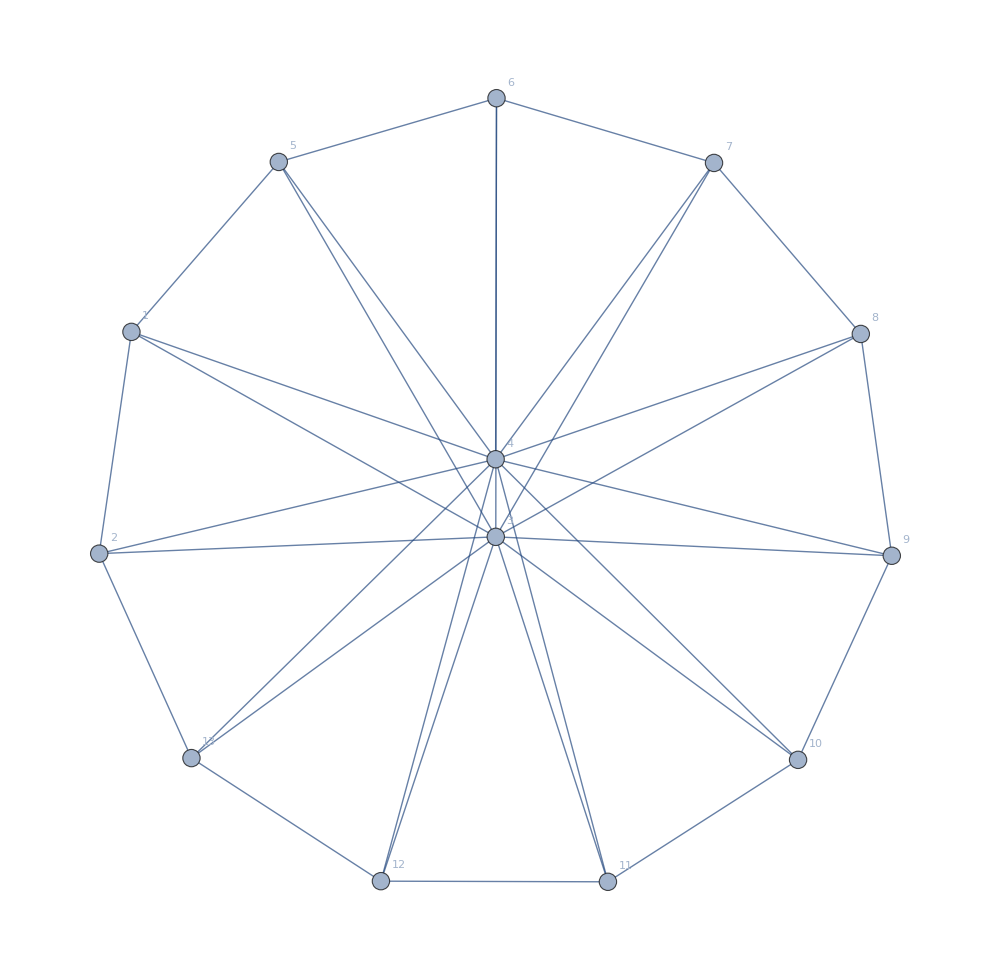

Graph[{1,2,3,4,5,13,6,7,8,9,10,11,12},{Null,{{1,2},{3,2},{3,1},{1,4},{2,4},{5,1},{6,2},{6,3},{5,4},{5,3},{7,5},{7,3},{7,4},{8,7},{8,3},{8,4},{9,8},{9,3},{9,4},{10,9},{10,3},{10,4},{11,10},{11,3},{11,4},{12,11},{12,3},{12,4},{13,12},{13,3},{13,4},{6,13},{6,4}}},{GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImageSize→{991.,Automatic},GraphHighlight→{3<->4},GraphLayout→{Dimension→2},VertexLabels→{Name}}]

{1<->2,1<->3,1<->5,2<->3,2<->5,2<->9,3<->4,3<->5,3<->6,3<->7,3<->8,3<->9,3<->10,3<->11,3<->12,4<->5,4<->11,5<->6,5<->7,5<->8,5<->9,5<->10,5<->11,5<->12,6<->10,6<->12,7<->9,7<->10,8<->11,8<->12}

{1,2,3,5,9,4,6,7,8,10,11,12}

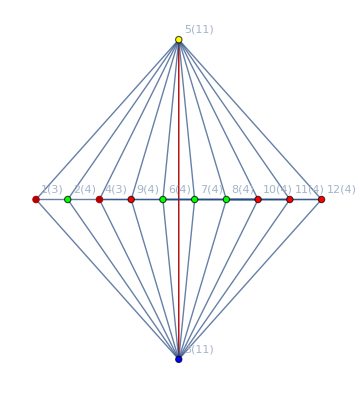

```mathematica
With[
{g=ReadGrof[9150]},
Print[Sort[EdgeList[g]]];
Print[VertexList[g]];PaintGraph2First[g,"x1==1&&x2==2&&x3==3", VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}],GraphHighlight->{1,4,3<->5},ImageSize->Medium, VertexCoordinates->{{1,0},{2,0},{5.5,-5},{5.5,5},{4,0},{3,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}]
]
```

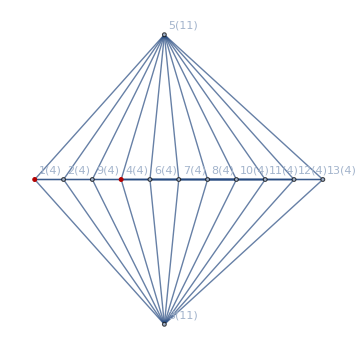
```mathematica
-Graphics--Graphics-
```

```mathematica
Table[{i,0},{i,Range[13]}]
```

```mathematica
{{1,0},{2,0},{4,-1},{4,1},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0}}
```

```mathematica
With[
{g=Rule2[ReadGrof[9150],3<->5,1<->4]},
Print[VertexList[g]];Graph[g, VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}],GraphHighlight->{1,4,3<->5},ImageSize->Medium]
]
```

{1,2,3,5,9,4,6,7,8,10,11,12,13}

```mathematica
With[
{g=ReadGrof[9150]},
Print[VertexList[g]];Graph[g, VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}],GraphHighlight->{1,4,3<->5},ImageSize->Medium]
]
```

{1,2,3,5,9,4,6,7,8,10,11,12}

-Graphics-

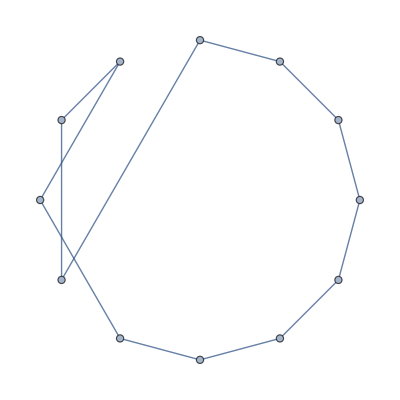

```mathematica
VertexDelete[JacobsThalGraph[10],{3,4}]
```

{1,2,3,4,5,14,6,7,8,9,10,11,12,13}

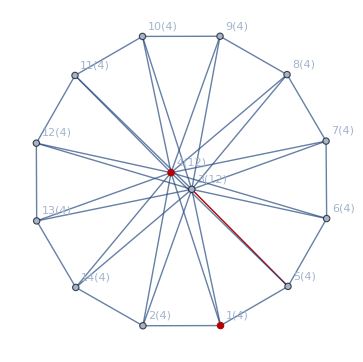

```mathematica
With[
{g=JacobsThalGraph[10]},
Print[VertexList[g]];Graph[g, VertexLabels->Table[v->{ToString[v]<>"("<>ToString[EdgeCount[g,v<->_]]<>")"},{v,VertexList[g]}],GraphHighlight->{1,4,3<->5},ImageSize->Medium]
]
```

```mathematica
Tally[{{6,0},{7,0},{6,5},{6,-5},{5,0},{9,0},{4,0},{3,0},{2,0},{1,0},{12,0},{11,0},{10,0},{9,0}}]
```

{{{6,0},1},{{7,0},1},{{6,5},1},{{6,-5},1},{{5,0},1},{{9,0},2},{{4,0},1},{{3,0},1},{{2,0},1},{{1,0},1},{{12,0},1},{{11,0},1},{{10,0},1}}

```mathematica
constrained12[x_]:=ChromaticPolynomial[ReadGrof[9150],x]
```

```mathematica
Table[(constrained12[k]/(k!/(k-3)!))^(1/9),{k,4,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

```mathematica
VertexCount[ReadGrof[9150]]
```

12